```mathematica
R[n_]:=(2Sqrt[2])/9801 Sum[((4 k)!(1103+26390k))/((k!)^4 396^(4 k)),{k,0,n}]
```

```mathematica
N[1/R[5]-π,100]
```

4.741011768567914974136850634834727161360394467082098721200536639730466696354233748949017936147287482×10^-48

```mathematica
Table[R[n],{n,10}]
```

{1130173253125/(2510613731736 √2),1029347477390786609545/(2286635172367940241408 √2),7766473062254307011793347201855/(17252765328978109815564789153792 √2),509299577881529611662930757403081523769055/(1131379202490552979877435552947122965839872 √2),57982950211280781944919792648021104999982386829481/(128805730098892711723125911845114081418091536842752 √2),3499871759747710499842768988784507373816789022688631739047925/(7774760263562699859971501015139525269727219309055349184528384 √2),398454856050409400033667498427037929849361304439288784703764447270125/(885144140786355895741177195716026970950416670420565960985448225439744 √2),6334387787708107824222495376281706107615730472323276284056009760393364218543125/(14071471712843535798792494970078253119671801362717159118900747103370578550063104 √2),14194592594146827909170805406080156403980453284185387917579020073045561359013099552859053125/(31532456625322022370765818276612583919584083811310999597255056965804073403194963043194765312 √2),116354295547844200479625540962705305445031010498388307062857519290687784871920308555177681218916232885/(258474257235476477051634224477005861793643791092488013501737085215352314477706263478530979938932097024 √2)}

```mathematica
Table[N[i/(2i+1),50],{i,100}]
```

```mathematica
P[n_,n_]:=1;
P[n_,i_]:=2+i/(2i+1)P[n,i+1]
```

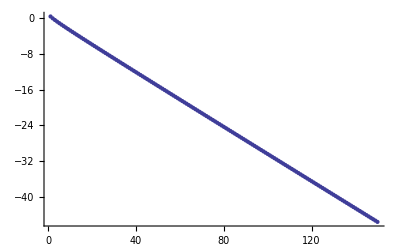

```mathematica
ListPlot[Table[Log[10,Abs[N[P[n,1]-π,500]]],{n,1,150}]]
```

```mathematica
m[k_]:={{k,4*k+2},{0,2*k+1}}
```

```mathematica
product[n_,n_]:=IdentityMatrix[2];
product[n_,i_]:=m[i].product[n,i+1]
product[n_]:=product[n,1]
```

```mathematica
x[0]=0;x[i_]:=(1+2i)(2(i-1)!+x[i-1])
```

```mathematica
product2[n_]:={{n!,x[n]},{0,Product[1+2i,{i,n}]}}
```

```mathematica
Table[product2[i]-product[i+1],{i,10}]
```

{{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}},{{0,0},{0,0}}}

```mathematica
2 Product[1+2i,{i,n}]
```

(2^(1-n) (1+2 n)!)/(n!)

```mathematica
reduce[m_,x_]:=(#[[1]])/(#[[2]])&[m.{x,1}]
```

```mathematica
P2[n_,x_]:=reduce[product2[n],x]
```

```mathematica
err[n_,x_]:=Log[10,Abs[N[P2[n,x]-π,500]]]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 72107338391763806435200425929334800145097482867124552655205713327418290257367227222400467362865517999180750505546389284420845568/22952478676498416711138029850063287872079204589138925981326030390833146152064944380459789310141526372662940068439977718408373625 - π.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 75254436255824244038351020955364147737165431613882337260130728906217430893033607022650306428733405206683642387384787533824/23954231039416745331537750640047880261152558452556678920903807489875892279589658527602541901465732673247926846448323459625 - π.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating 57717787076305760275598872079534922732535652392672502347116784378594273248701063249816673813936950729301912513476906411113815474176/18372142235039150700897321040803936998852644630719448178527968621200164379784836709257543158135742757344481552815062164864355065375 - π.

General::stop: Further output of N :: meprec will be suppressed during this calculation.

$RecursionLimit::reclim: Recursion depth of 256 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

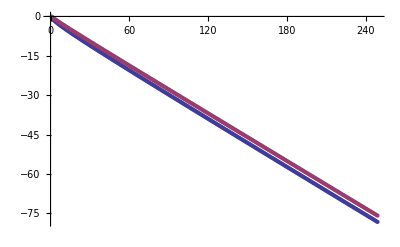

```mathematica
ListPlot[Table[err[n,#],{n,1,250}]&/@{4,6}]
```

```mathematica
Simplify[{{A[1,1],A[1,2]},{0,A[2,2]}}.m[i]]//MatrixForm
```

(i A[1,1] | (1+2 i) (2 A[1,1]+A[1,2])
0 | (1+2 i) A[2,2])

```mathematica
product[200]
```

product[200]

```mathematica
Exit[]
```

```mathematica
RSolve[x[i+1]==(3+2 i) (2 i!+x[i]),x[i],i]
```

{{x[i]→2^(-1+i) C[1] Pochhammer[5/2,-1+i]+3 2^(-1+i) √π (√π-(2^-i i! Hypergeometric2F1[1,1+i,3/2+i,1/2])/((1/2 (1+2 i))!)) Pochhammer[5/2,-1+i]}}